# Break-even point of phase-flip code

## Description

In this notebook, we investigate when the phase-flip repetition code is getting more advantageous than a single physical qubit against a certain noise model.
We study the repetition code under realistic noise models such as amplitude damping (characterised by relaxation time T_1) and phase damping (dephasing time T_2). The time-evolution of density matrix is described by Kraus formalism.
We derive a break-even point, above which the repetition code is effective and preserves arbitrary quantum data even longer than a single qubit lifetime.

## Definitions

```mathematica
$Assumptions=T1>0&&T2>0&&T2s>0&&t>0&&θ∈Reals&&ϕ∈Reals;

(* Kraus operators describe qubit relaxation and dephasing *)
K1phase={{√(1-α),0},{0,√(1-γ)}};
K2phase={{√α,0},{0,0}} ;
K2relax={{0,√γ},{0,0}};

(* CNOT gate *)
Ν=3;
basis=Tuples[{0,1},Ν];
CNOTket[i_,j_,list_]:=Block[{output=list},If[list⟦i⟧==0,output,output⟦j⟧=-output⟦j⟧+1;output]]
CNOTmatrix[i_,j_]:=Normal[SparseArray[Table[{n,Position[basis,CNOTket[i,j,basis⟦n⟧]]⟦1,1⟧}->1,{n,Length[basis]}],{Length[basis],Length[basis]}]]
Do[CNOT[i->j]=CNOTmatrix[i,j],{i,Ν},{j,Ν}]

(* Toffoli gate *)
CCNOTket[i_,j_,k_,list_]:=Block[{out=list},If[list⟦i⟧==0||list⟦j⟧==0,out,out⟦k⟧=-out⟦k⟧+1;out]]
CCNOTmatrix[i_,j_,k_]:=Normal[SparseArray[Table[{n,Position[basis,CCNOTket[i,j,k,basis⟦n⟧]]⟦1,1⟧}->1,{n,Length[basis]}],{Length[basis],Length[basis]}]]
Do[CCNOT[i->j->k]=CCNOTmatrix[i,j,k],{i,Ν},{j,Ν},{k,Ν}]

(* Partial trace *)
PartialTrace[ρ_,dim_]:=Block[{Ν,ρs},
Ν=Log[2,Length[ρ]];
ρs=ArrayReshape[ρ,ConstantArray[2,2Ν]];
ArrayReshape[TensorContract[ρs,Map[{#,#+Ν}&,dim]],{2^(Ν-Length[dim]),2^(Ν-Length[dim])}]]

(* 3-qubit Hadamard *)
H3=KroneckerProduct[HadamardMatrix[2],HadamardMatrix[2],HadamardMatrix[2]];
```

## Single qubit

```mathematica
(* initial state and initial density matrix *)
ψ0=Cos[θ/2] {1,0}+Sin[θ/2] ⅇ^(ⅈ ϕ) {0,1};
ρ0=Refine[Outer[Times, ψ0,Conjugate[ψ0]],{ϕ∈Reals,θ ∈Reals}];
```

```mathematica
(* Relaxation and dephasing error channel by Kraus formalism *)
ρ1t=(#.ρ0.ConjugateTranspose[#])&/@{K1phase,K2phase,K2relax}//Total;
%//MatrixForm;
```

```mathematica
(* To quantify the effect of errors, fidelity is calculated and averaged over the Bloch spehere *)
F1=Conjugate[ψ0].(ρ1t).ψ0/.{γ->(1-ⅇ^(-t/T1)),α->(1-ⅇ^(-2t/T2s))};
```

```mathematica
Favg=Integrate[1/(4 π)*(F1)*Sin[θ],{ϕ,0,2π},{θ,0,π}]/.T2s->2T1*T2/(2T1-T2)//Simplify
```

1/6 (3+ⅇ^(-t/T1)+2 ⅇ^(-t/T2))

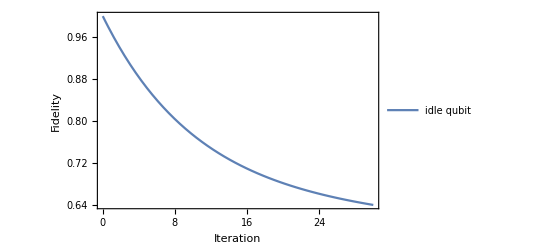

```mathematica
Plot[Favg/.{T1->100, T2->10},{t,0,30},Frame->True,FrameLabel->{"Iteration","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->400,Axes->False,FrameStyle->Directive[Black],PlotLegends->{"idle qubit"}]
```

## 3-qubit repetition phase-flip code

Error correction scheme is sketched below.

-Graphics-

The quantum circuit of our scheme is realised in the following way:
1) initially 1 qubit holds the quantum data we want to preserve
2) other 2 qubits are in their ground state
3) we apply CNOTs gates for encoding
4) Hadamard gates are applied on each qubits
5) idling time, while we want to preserve the data, errors act here
6) again applying Hadamards
7) other CNOTs for recalling the state into 1 qubit
8) Toffoli gate is applied for error correction
9) reset the ancillary qubits

```mathematica
ρ init=KroneckerProduct[ρ0,DiagonalMatrix[{1,0,0,0}]];
ρ enc=CNOT[1->2].CNOT[1->3].ρ init.ConjugateTranspose[CNOT[1->2].CNOT[1->3]];
ρ H=H3.ρ enc.H3;
ops=Flatten[Table[KroneckerProduct[q1,q2,q3],{q1,{K1phase,K2phase,K2relax}},{q2,{K1phase,K2phase,K2relax}},{q3,{K1phase,K2phase,K2relax}}],2];
ρ3t=Total[Map[#.ρ H.ConjugateTranspose[#]&,ops]];
ρ3tH=H3.ρ3t.H3;
ρ recall=CNOT[1->2].CNOT[1->3].ρ3tH.ConjugateTranspose[CNOT[1->2].CNOT[1->3]];
ρ cor=CCNOT[3->2->1].ρ recall.ConjugateTranspose[CCNOT[3->2->1]];
ρ1t′=PartialTrace[ρ cor,{2,3}];
```

```mathematica
F3=Conjugate[ψ0].(ρ1t′).ψ0/.{γ->(1-ⅇ^(-t/T1)),α->(1-ⅇ^(-2t/T2s))};
```

```mathematica
Favg3=Integrate[1/(4 π)*(F3)*Sin[θ],{ϕ,0,2π},{θ,0,π}]/.T2s->2T1*T2/(2T1-T2)//FullSimplify
```

1/12 (6+2 ⅇ^(-(3 t)/T1)-2 ⅇ^(-(3 t)/T2)+3 ⅇ^(-t (2/T1+1/T2)) (1+ⅇ^((2 t)/T1)))

```mathematica
(* break-even point when phase-flip code gets more advantegous than a single physical qubit *)
p1=Normal[Series[Favg,{t,0,1}]];
p2=Normal[Series[Favg3,{t,0,1}]];
Reduce[(p1<p2)/.T2->2 T1 T2s/(2 T1+T2s)//Simplify,T1];
%[[2]]
```

T1>2 T2s

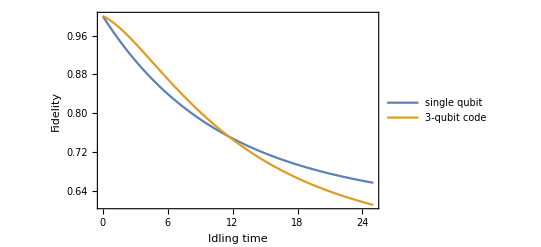

```mathematica
(* plotting a specific scenario when repetition code is beneficial (T1 > 2T2s) up to a treshold t′ time *)
Plot[{Favg/.{T1->100, T2->10},Favg3/.{T1->100, T2->10}},{t,0,25},Frame->True,FrameLabel->{"Idling time","Fidelity"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->400,Axes->False,FrameStyle->Directive[Black],PlotLegends->{"single qubit","3-qubit code"}]
```

## Optimal code-length

```mathematica
Clear[p,p0,NN];
falso=1/2*ⅇ^(ⅈ*ϕ)*Sum[Binomial[NN,k]p0^k*(p)^(NN-k),{k,0,(NN-1)/2}]+1/2*ⅇ^(-ⅈ*ϕ)*Sum[Binomial[NN,k]p^k*(p0)^(NN-k),{k,0,(NN-1)/2}]-γ^NN/2//FullSimplify;
matr={{1/2,falso/.{ϕ->-ϕ}},{falso,1/2}};
f0=1/2{1,ⅇ^(-ⅈ*ϕ)}.(matr.{1,ⅇ^(ⅈ*ϕ)})//Simplify;
(f0/.{ϕ->0})+(f0/.{ϕ->π/2})+(f0/.{ϕ->π})+(f0/.{ϕ->3π/2})//Simplify;
fidelity=(%+2*Sum[Binomial[NN,k]((1-p+p0)/2)^k*(1-((1-p+p0)/2))^(NN-k),{k,0,(NN-1)/2}])/6//FullSimplify;
fidelity/.{NN->3,γ->1-ⅇ^(-t/T1),
p->(ⅇ^(-t/T1)+ⅇ^(-t/T2))/2,
p0->(ⅇ^(-t/T1)-ⅇ^(-t/T2))/2}//Simplify;
```

```mathematica
NMax=9;
Table[fid[i]=fidelity/.{NN->i,γ->1-ⅇ^(-t/T1),
p->(ⅇ^(-t/T1)+ⅇ^(-t/T2))/2,
p0->(ⅇ^(-t/T1)-ⅇ^(-t/T2))/2}/.T2->2 T1 T2s/(2 T1+T2s)/.T2s->1//Simplify,{i,1,NMax,2}];

fids=Table[{i,fid[i]},{i,1,NMax,2}];

g[t′_,T1′_]:=Block[{},MaximalBy[fids/.{t->N[t′],T1->N[T1′]},Last]⟦1,1⟧]
```

```mathematica
bl=BarLegend[{{"SunsetColors","Reverse"},{0,10}},{3,5,7,9}, LegendLabel->Placed["Qubit number",Right,Rotate[#,90 Degree]&],LegendMarkerSize->250];
DensityPlot[g[t,log10T1],{log10T1,1,100},{t,0,2},PlotPoints->50,MaxRecursion->5, PlotLegends->bl, ImageSize->350,FrameLabel->{"T1/T2*","t/T2*"},ColorFunction->ColorData[{"SunsetColors","Reverse"}],LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},FrameStyle->Directive[Black], PlotRange->All, ScalingFunctions->{"Log10",None}]
```

-Graphics-